## functions

```mathematica
ToStringWithDateCorrection[expression_]:=If[
Length[StringSplit[ToString[expression],""]]==1,
"0"<>ToString[expression],
ToString[expression]
]
ToStringWithDateCorrection[expression_,correctLength_]:=If[
Length[StringSplit[ToString[expression],""]]<correctLength,
StringRiffle[ConstantArray["0",correctLength-Length[StringSplit[ToString[expression],""]]],""]<>ToString[expression],
ToString[expression]
]
```

```mathematica
MinuteOfDayToHourAndMinuteString[minuteOfDay_]:=ToStringWithDateCorrection[IntegerPart[minuteOfDay/60]]<>":"<>ToStringWithDateCorrection[FractionalPart[minuteOfDay/60]60]
MinuteOfDayToHourAndMinuteList[minuteOfDay_]:={IntegerPart[minuteOfDay/60],FractionalPart[minuteOfDay/60]60}
```

```mathematica
HourAndMinuteToMinuteOfDay[hour_,minute_]:=60hour+minute
```

```mathematica
HourAndMinuteToMinuteOfDay[hourAndMinuteString_]:=If[
StringContainsQ[hourAndMinuteString,":"],
StringSplit[hourAndMinuteString,":"]//ToExpression[#[[1]]]60+ToExpression[#[[2]]]&,
ToExpression[StringTake[hourAndMinuteString,{1,2}]]60+ToExpression[StringTake[hourAndMinuteString,{3,4}]]
]
```

```mathematica
DateExtend[dateObject_,hour_,minute_]:=DateObject[Flatten[{DateList[dateObject][[1;;3]],{hour,minute}}]]
```

```mathematica
(*Function to normalize DateObjects to the same granularity*)
NormalizeDate[date_]:=DateObject[DateList[date][[1;;3]]]

(*Function to find the index of the first element not less than a given date*)
FindFirstIndexNotLessThan[list_,date_]:=Module[{len=Length[list],low=1,high,mid,normDate},normDate=NormalizeDate[date];
high=len;
While[low<high,mid=Quotient[low+high,2];
If[NormalizeDate[First[list[[mid]]]]<normDate,low=mid+1,high=mid];];
low]

(*Function to find the index of the first element greater than a given date*)
FindFirstIndexGreaterThan[list_,date_]:=Module[{len=Length[list],low=1,high,mid,normDate},normDate=NormalizeDate[date];
high=len;
While[low<high,mid=Quotient[low+high,2];
If[NormalizeDate[First[list[[mid]]]]<=normDate,low=mid+1,high=mid];];
low]

(*Define the function to select elements by date range*)
SelectElementsByDateRange[list_,startDate_,endDate_]:=Module[{startIndex,endIndex,normStartDate,normEndDate},(*Normalize dates*)normStartDate=NormalizeDate[startDate];
normEndDate=NormalizeDate[endDate];
(*Find the starting and ending indices*)startIndex=FindFirstIndexNotLessThan[list,normStartDate];
endIndex=FindFirstIndexGreaterThan[list,normEndDate];
(*Return the sublist within the range*)list[[startIndex;;endIndex-1]]]
```

## misc

## heatmeter read-in

```mathematica
ToStringWithDateCorrection[expression_]:=If[
Length[StringSplit[ToString[expression],""]]==1,
"0"<>ToString[expression],
ToString[expression]
]
ToStringWithDateCorrection[expression_,correctLength_]:=If[
Length[StringSplit[ToString[expression],""]]<correctLength,
StringRiffle[ConstantArray["0",correctLength-Length[StringSplit[ToString[expression],""]]],""]<>ToString[expression],
ToString[expression]
]
```

```mathematica
MinuteOfDayToHourAndMinute[minuteOfDay_]:=ToStringWithDateCorrection[IntegerPart[minuteOfDay/60]]<>":"<>ToStringWithDateCorrection[FractionalPart[minuteOfDay/60]60]
```

```mathematica
HourAndMinuteToMinuteOfDay[hour_,minute_]:=60hour+minute
```

```mathematica
HourAndMinuteToMinuteOfDay[hourAndMinuteString_]:=If[
StringContainsQ[hourAndMinuteString,":"],
StringSplit[hourAndMinuteString,":"]//ToExpression[#[[1]]]60+ToExpression[#[[2]]]&,
ToExpression[StringTake[hourAndMinuteString,{1,2}]]60+ToExpression[StringTake[hourAndMinuteString,{3,4}]]
]
```

```mathematica
rawDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\raw";
```

```mathematica
formattedDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\formatted";
```

```mathematica
path=formattedDataRoot;
fileName="heat_stock_net.csv";
lastLoadDay=Module[
{dirs,sortedDirs,foundFile},
(*Get list of directories*)
dirs=FileNames["*",path];
(*Sort directories in decreasing order*)
sortedDirs=Sort[dirs,DateObject[#1]>DateObject[#2]&];
(*Search for the file*)
foundFile=SelectFirst[sortedDirs,FileExistsQ[FileNameJoin[{#,fileName}]]&];
StringSplit[foundFile,"\\"][[-1]]
];
loadDayStamps=Map[StringRiffle[Map[ToStringWithDateCorrection,#[[1;;3]]],"-"]&,DateRange[{2024,2,1},DateObject[lastLoadDay]]];
heatStockDataOriginal=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_stock.csv"]&,
loadDayStamps]]/.{$Failed->"no data"};
heatStockDataNet=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_stock_net.csv"]&,
loadDayStamps]]/.{$Failed->"no data"};
badDays=Flatten[Intersection[Flatten[Position[heatStockDataOriginal,$Failed]],Flatten[Position[heatStockDataNet,$Failed]]]];
goodDays=Complement[Range[Length[loadDayStamps]],badDays];
Manipulate[
Module[
{dayN,timeStamps},
dayN=Position[loadDayStamps,day][[1]][[1]];
timeStamps=Map[
HourAndMinuteToMinuteOfDay[StringTake[#,{-10,-7}]]&,
Select[FileNames[All,rawDataRoot<>"\\"<>day<>"\\heatmeter_images\\"],StringEndsQ[#,".png"]&]
];
Grid[{
{"day","original","net","diff"},
{
loadDayStamps[[dayN]],
If[Dimensions[heatStockDataOriginal[[dayN]]]!={},heatStockDataOriginal[[dayN]][[-1]][[2;;5]],"no data"],
If[Dimensions[heatStockDataNet[[dayN]]]!={},heatStockDataNet[[dayN]][[-1]][[2;;5]],"no data"],
If[Dimensions[heatStockDataOriginal[[dayN]]]!={}&&Dimensions[heatStockDataNet[[dayN]]]!={},heatStockDataNet[[dayN]][[-1]][[2;;5]]-heatStockDataOriginal[[dayN]][[-1]][[2;;5]],"no data"]
},
Table[ListPlot[
{
If[Dimensions[heatStockDataOriginal[[dayN]]]!={},Transpose[Transpose[heatStockDataOriginal[[dayN]]][[{1,1+cycle}]]],Nothing],
If[Dimensions[heatStockDataNet[[dayN]]]!={},Transpose[Transpose[heatStockDataNet[[dayN]]][[{1,1+cycle}]]],Nothing]
},
Joined->True,PlotRange->All,Ticks->{Map[{#,Rotate[MinuteOfDayToHourAndMinute[#],Pi 0.25]}&,Range[0,24 60, 120]],Automatic},ImageSize->250,PlotLabel->"cycle "<>ToString[cycle],Prolog->{If[showCaptures,{Pink,Thin,Map[Line[{{#,0},{#,10000}}]&,timeStamps]}]}
],{cycle,1,4}]
}]
],
{showCaptures,{False,True}},
{{day,loadDayStamps[[goodDays]][[-1]]},loadDayStamps[[goodDays]]}
]
```

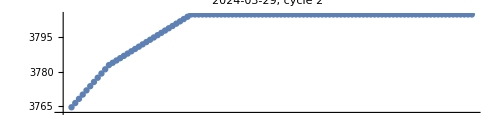
-Graphics-
1500 | 1510 | 1520 | 1530 | 1540 | 1550 | 1600 | 1610 | 1620 | 1630 | 1640 | 1650 | 1700 | 1710 | 1720 | 1730 | 1740 | 1750 | 1800 | 1810 | 1820 | 1830 | 1840 | 1850 | 1900 | 1910 | 1920 | 1930 | 1940 | 1950 | 2000 | 2010 | 2020 | 2030 | 2040 | 2050 | 2100 | 2110 | 2120 | 2130 | 2140 | 2150 | 2200 | 2210 | 2220 | 2230 | 2240 | 2250 | 2300 | 2310 | 2320 | 2330 | 2340 | 2350
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
cycle=2;timeSpan={15,24}100;
day=loadDayStamps[[goodDays]][[-1]];
dayN=Position[loadDayStamps,day][[1]][[1]];
timeStamps=DeleteDuplicates[Map[
ToExpression[StringTake[#,{-10,-7}]]&,
Select[FileNames[All,rawDataRoot<>"\\"<>day<>"\\heatmeter_images\\"],StringEndsQ[#,".png"]&]
]];
cycleImagesForTimeSpan=Map[
Import[rawDataRoot<>"\\"<>day<>"\\heatmeter_images\\"<>ToStringWithDateCorrection[#,4]<>"_"<>ToString[cycle]<>".png"]
&,Select[timeStamps,Between[#,timeSpan]&]];
{
ListPlot[
{
If[Dimensions[heatStockDataOriginal[[dayN]]]!={},Select[Transpose[Transpose[heatStockDataOriginal[[dayN]]][[{1,1+cycle}]]],Between[#[[1]],Map[HourAndMinuteToMinuteOfDay,Map[ToStringWithDateCorrection[#,4]&,timeSpan]]]&],Nothing],
If[Dimensions[heatStockDataNet[[dayN]]]!={},Select[Transpose[Transpose[heatStockDataNet[[dayN]]][[{1,1+cycle}]]],Between[#[[1]],Map[HourAndMinuteToMinuteOfDay,Map[ToStringWithDateCorrection[#,4]&,timeSpan]]]&],Nothing]
},
Ticks->{Map[{#,Rotate[MinuteOfDayToHourAndMinute[#],Pi 0.5]}&,Range[0,24 60, 10]],Automatic},ImageSize->500,AspectRatio->0.25,PlotLabel->day<>", cycle "<>ToString[cycle]
],
{Select[timeStamps,Between[#,timeSpan]&],cycleImagesForTimeSpan}//Grid
}//Column
```

```mathematica
heatFlowDataOriginal=Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_flow.csv"]&,
loadDayStamps];
```

```mathematica
heatFlowDataNet=Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_flow_net.csv"]&,
loadDayStamps];
```

```mathematica
Table[
Table[
ListPlot[
{
Transpose[Transpose[heatFlowDataOriginal[[day]]][[{1,1+cycle}]]],
Transpose[Transpose[heatFlowDataNet[[day]]][[{1,1+cycle}]]]
},
Joined->True,PlotRange->All
]
,{cycle,1,4}]
,{day,goodDays}]//Grid
```

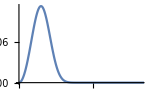
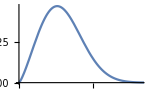
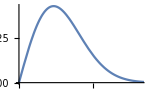
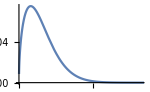

```mathematica
weibullParameters={
{3,10.3,0.001},
{2.3,20,0.001},
{2,20,0.001},
{1.5,10,0.001}
};
Table[Plot[
PDF[WeibullDistribution[weibullParameters[[cycle]][[1]],weibullParameters[[cycle]][[2]],weibullParameters[[cycle]][[3]]],power],{power,0,100},PlotRange->{{0,50},All},ImageSize->150
],{cycle,1,4}]//Row
```

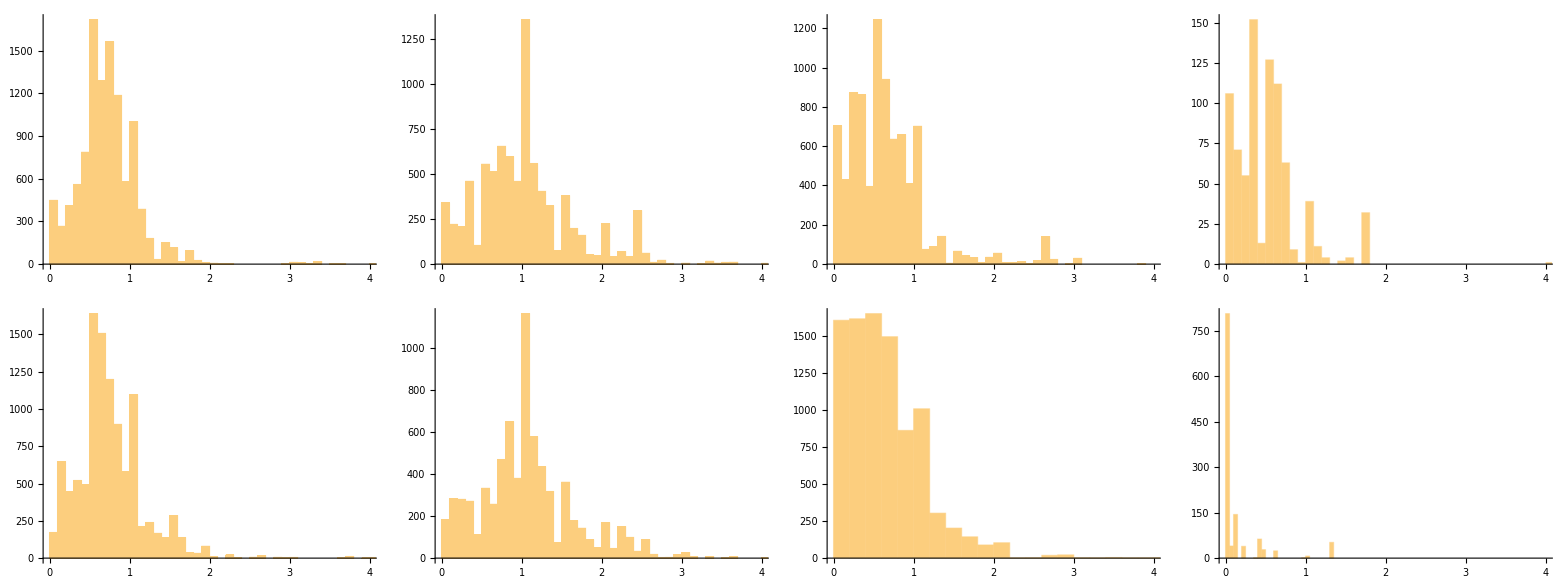

```mathematica
{
Table[
Histogram[
Select[Flatten[Table[
Differences[Transpose[heatStockDataOriginal[[dayN]]][[1+cycle]]]
,{dayN,goodDays}]],0.01<#<100&],PlotRange->{{0,4},All}
],{cycle,1,4}],
Table[
Histogram[
Select[Flatten[Table[
Differences[Transpose[heatStockDataNet[[dayN]]][[1+cycle]]]
,{dayN,goodDays}]],0.01<#<100&],PlotRange->{{0,4},All}
],{cycle,1,4}]
}//Grid
```

## adatok

```mathematica
rawDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\raw";
```

```mathematica
formattedDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\formatted";
```

```mathematica
seasonDays=Map[DateObject,DateRange[{2023,11,8},{2024,5,16}]];
```

## hő

```mathematica
heatDataDays=Map[DateObject,DateRange[{2023,11,22},{2024,3,29}]];
```

```mathematica
heatStockPre=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_stock_net.csv"]&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,heatDataDays]]];
```

```mathematica
heatStockDated=Map[Flatten[#,1]&,Transpose[Table[
Module[
{dayDateList},
dayDateList=DateList[heatDataDays[[dayN]]];
Transpose[Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[heatStockLine[[1]]];
Transpose[{ConstantArray[DateObject[dayDateList],4],heatStockLine[[2;;5]]}]
,{heatStockLine,heatStockPre[[dayN]]}]]
]
,{dayN,1,Length[heatDataDays]}]]];
(*1-es kör átfordulás: jan 20-21*)
(*2-es kör átfordulás: feb 4-5*)
```

```mathematica
cycle=2;
Map[
SortBy[heatStock[[cycle]][[#[[1]];;#[[1]]+1]],First]&,
Map[Position[Differences[Transpose[heatStockDated[[cycle]]][[2]]],#][[1]]&,Select[Differences[Transpose[heatStockDated[[cycle]]][[2]]],#<-10&]]
]
```

{{{Thu 14 Dec 2023 23:55:00GMT+2,4247},{Fri 15 Dec 2023 00:00:00GMT+2,4228.81}},{{Sun 4 Feb 2024 23:55:00GMT+2,9937},{Mon 5 Feb 2024 00:00:00GMT+2,125.}}}

```mathematica
heatStockDated[[1]]=Map[
If[
DateObject[{2024,1,20,23,59}]<#[[1]],
{#[[1]],#[[2]]+10000},
#
]
&,heatStockDated[[1]]];
```

```mathematica
heatStockDated[[2]]=Quiet[Map[
If[
DateObject[{2024,2,4,23,59}]<=#[[1]],
{#[[1]],#[[2]]+10000},
#
]
&,heatStockDated[[2]]]];
```

```mathematica
Export[NotebookDirectory[]<>"\\heatStockDated.mx",heatStock];
```

```mathematica
heatStockSeason=Table[
Transpose[{
Transpose[heatStockDated[[cycle]]][[1]],
Transpose[heatStockDated[[cycle]]][[2]]-heatStockDated[[cycle]][[1]][[2]]
}],{cycle,1,4}];
```

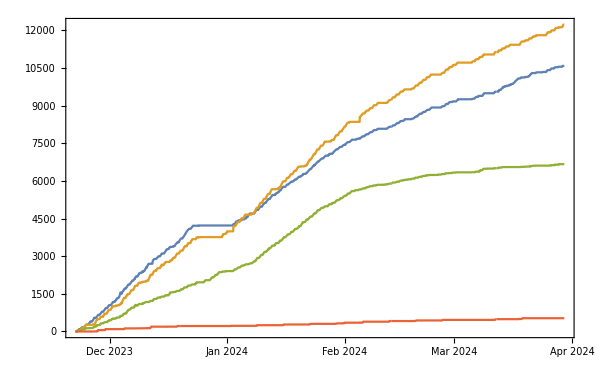

```mathematica
DateListPlot[heatStockSeason]
```

```mathematica
Export[NotebookDirectory[]<>"\\heatStockSeason.mx",heatStockSeason];
```

```mathematica
heatStockSeason=Import[NotebookDirectory[]<>"\\heatStockSeason.mx"];
```

```mathematica
heatStockDaily=Table[Table[
Module[
{dailyCumulative},
dailyCumulative=SelectElementsByDateRange[heatStockSeason[[cycle]],DateExtend[day,0,0],DateExtend[day,23,59]];
If[
dailyCumulative!={},
Transpose[{
Transpose[dailyCumulative][[1]],
Transpose[dailyCumulative][[2]]-dailyCumulative[[1]][[2]]
}],
None]
]
,{day,seasonDays}],{cycle,1,4}];
```

```mathematica
Export[NotebookDirectory[]<>"\\heatStockDaily.mx",heatStockDaily];
```

```mathematica
heatStockDaily=Import[NotebookDirectory[]<>"\\heatStockDaily.mx"];
```

## gáz

```mathematica
gasDataDays=Map[DateObject,Join[
DateRange[{2023,11,23},{2023,12,6}],
DateRange[{2023,12,15},{2024,5,16}]
]];
```

```mathematica
gasStockPre=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\gas_stock.csv"]&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,gasDataDays]]];
```

```mathematica
gasStockDaily=Table[
If[
MemberQ[gasDataDays,day],
Module[
{dayN,dayDateList},
dayN=Position[gasDataDays,day][[1]][[1]];
dayDateList=DateList[gasDataDays[[dayN]]];
Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[gasStockLine[[1]]];
Transpose[{DateObject[dayDateList],gasStockLine[[2]]}]
,{gasStockLine,gasStockPre[[dayN]]}]
],
None
]
,{day,seasonDays}];
```

```mathematica
Export[NotebookDirectory[]<>"\\gasStockDaily.mx",gasStockDaily];
```

```mathematica
gasStockDaily=Import[NotebookDirectory[]<>"\\gasStockDaily.mx"];
```

## szobák hőmérséklete

```mathematica
roomTempDataDays=Map[DateObject,DateRange[{2023,11,8},{2024,5,16}]];
```

```mathematica
roomTempsPre=Table[Quiet[
Map[
Import[formattedDataRoot<>"\\"<>#<>"\\room_"<>ToString[room]<>"_temps.csv"]
&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,roomTempDataDays]]
],{room,1,10}];
```

```mathematica
roomTempsDaily=Table[Table[
If[
MemberQ[roomTempDataDays,day],
Module[
{dayN,dayDateList},
dayN=Position[roomTempDataDays,day][[1]][[1]];
dayDateList=DateList[roomTempDataDays[[dayN]]];
If[
Dimensions[roomTempsPre[[room]][[dayN]]]!={},
Transpose[Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[roomTempLine[[1]]];
Transpose[{ConstantArray[DateObject[dayDateList],4],roomTempLine[[2;;5]]}]
,{roomTempLine,roomTempsPre[[room]][[dayN]]}]],
None
]
],
None
]
,{day,seasonDays}],{room,1,10}];
```

```mathematica
Export[NotebookDirectory[]<>"\\roomTempsDaily.mx",roomTempsDaily];
```

```mathematica
roomTempsDaily=Import[NotebookDirectory[]<>"\\roomTempsDaily.mx"];
```

```mathematica
setTempLowForAtLeastOneRoomDaily=Transpose[
{roomTempDataDays,
Quiet[Map[
Min[#]<0&,
Transpose[Table[
Table[
Min[Select[Transpose[roomTemp[[1]]][[2]]-Transpose[roomTemp[[2]]][[2]],NumberQ]]
,{roomTemp,roomTempsDaily[[room]]}]
,{room,1,10}]]
]]
}];
```

## fűtési állapot

```mathematica
heatingStateDataDays=Map[DateObject,DateRange[{2023,11,8},{2024,5,16}]];
```

```mathematica
heatingStatePre=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heating_state.csv"]&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,heatingStateDataDays]]];
```

```mathematica
heatingStateDaily=Table[
If[
MemberQ[heatingStateDataDays,day],
Module[
{dayN,dayDateList},
dayN=Position[heatingStateDataDays,day][[1]][[1]];
dayDateList=DateList[heatingStateDataDays[[dayN]]];
If[
Dimensions[heatingStatePre[[dayN]]]!={},
Transpose[Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[heatingStateLine[[1]]];
Transpose[{ConstantArray[DateObject[dayDateList],5],heatingStateLine[[2;;6]]}]
,{heatingStateLine,heatingStatePre[[dayN]]}]],
None
]
],
None
]
,{day,seasonDays}];
```

```mathematica
Position[heatingStateDaily,None]
```

{{56},{57},{96},{97},{110},{111},{119},{120},{138},{145},{146},{152},{153},{154},{157},{158},{159},{160},{161},{162},{163},{167},{168},{173},{174},{175},{179},{180},{181},{182},{183},{184},{185},{186},{187},{188},{189},{190},{191},{192}}

```mathematica
heatingStateNoDataDays=heatingStateDataDays[[Flatten[Position[heatingStatePre,$Failed]]]];
```

```mathematica
noHeatingDays=Transpose[Select[setTempLowForAtLeastOneRoomDaily,#[[2]]==False&]][[1]];
```

```mathematica
Table[
Module[
{dayDateList,minutes,blankDayData,dayPosition},
dayDateList=DateList[day];
minutes=Map[
DateObject[Join [dayDateList[[1;;3]],MinuteOfDayToHourAndMinuteList[#]]]&
,Transpose[heatingStatePre[[1]]][[1]]];
blankDayData=ConstantArray[
Transpose[
{
minutes,
ConstantArray[0,288]
}
],5];
dayPosition=Position[seasonDays,day][[1]][[1]];
heatingStateDaily[[dayPosition]]=blankDayData;
]
,{day,Intersection[heatingStateNoDataDays,noHeatingDays]}]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Position[heatingStateDaily,None]
```

{{95},{96},{109},{110},{153},{162},{166},{167},{172},{174}}

```mathematica
Export[NotebookDirectory[]<>"\\heatingStateDaily.mx",heatingStateDaily];
```

```mathematica
heatingStateDaily=Import[NotebookDirectory[]<>"\\heatingStateDaily.mx"];
```

## egyéb

### külső hőmérséklet

```mathematica
externalTempDataDays=Complement[Map[DateObject,DateRange[{2023,11,23},{2024,5,16}]],{DateObject[{2024,1,1,0,0,0.}],DateObject[{2024,3,4,0,0,0.}]}];
```

```mathematica
externalTempPre=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\external_temp.csv"]&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,externalTempDataDays]]];
```

```mathematica
externalTempDaily=Table[
If[
MemberQ[externalTempDataDays,day],
Module[
{dayN,dayDateList},
dayN=Position[externalTempDataDays,day][[1]][[1]];
dayDateList=DateList[externalTempDataDays[[dayN]]];
Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[externalTempLine[[1]]];
Transpose[{DateObject[dayDateList],externalTempLine[[2]]}]
,{externalTempLine,externalTempPre[[dayN]]}]
],
None
]
,{day,seasonDays}];
```

```mathematica
Export[NotebookDirectory[]<>"\\externalTempDaily.mx",externalTempDaily];
```

```mathematica
externalTempDaily=Import[NotebookDirectory[]<>"\\externalTempDaily.mx"];
```

### környezeti változók

```mathematica
energyContentInGasPerCubicMeter=1000 34/3600;(*kWh*)
```

```mathematica
airSpecificMass=1.2;(*kg/m3*)
```

```mathematica
airSpecificHeatCapacity=1012;(*J/kg/K*)
```

```mathematica
roomNames={"ovi","PK","SZGK","Gólyairoda","Mérce","vendégtér","kisterem","trafóház","Oktopusz","Lahmacun","Kazán közös terek","műhely"};
```

```mathematica
roomToCycle={1,1,2,2,2,3,3,4,1,2};
```

```mathematica
roomAreas={53,26,29,26.5,72,100,60.25,240,66,24,50,26.5} ;
```

```mathematica
roomExternalWallLength={9.8,4.8,5.4,6,10.2,15.4,10.2,25,12.5,5.2,None,2.5} ;
```

```mathematica
roomHeight=3.2;
```

```mathematica
radiatorHeight=0.6;
roomRadiatorLength={4 140,280,300,180,540+150,6 120,4 120,0,2 140,100}/100;
```

## elemzés

## jegyzetek

úgy érdemes tekinteni, mint egy cél felé hajtott rendszert

kontrollváltozók:
	- fő kontrollváltozók: fogyasztott gáz és kiküldött hő
		> korrellált kontrollváltozók: fűtési állapot
	- nem irányított kontrollváltozó: kinti hőmérséklet, besugárzás
függő változók: szobák hőmérséklete

hibajel: beállított hőmérséklet - aktuális hőmérséklet

fő kérdések:
- milyen költséggel milyen mértékben lehet csökkenteni a hibát?
- hogy teljesít a rendszer, lehet-e jellemezni valahogy?
- külső körülmények hogyan befolyásolják?
- van-e olyan szcenárió, amivel jelentősen jobban teljesítene?
- lehet-e jellemezni a szobákat?
- hogyan viszonyul a tavalyi adatokhoz?

## hatékonyság

```mathematica
gasAndHeatStockDaily=Table[
Module[
{gasDataPosition,heatDataPosition},
gasDataPosition=Position[gasDataDays,day][[1]][[1]];
heatDataPosition=Position[heatDataDays,day][[1]][[1]];
{
gasStockDaily[[gasDataPosition]],
Table[heatStockDaily[[cycle]][[heatDataPosition]],{cycle,1,4}]
}
],{day,Intersection[gasDataDays,heatDataDays]}];
```

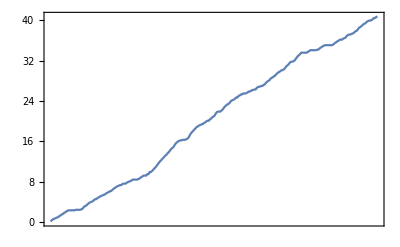

```mathematica
DateListPlot[gasAndHeatStockDaily[[1]][[1]]]
```

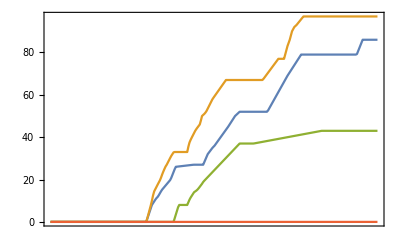

```mathematica
DateListPlot[gasAndHeatStockDaily[[1]][[2]]]
```

```mathematica
totalGasTotalHeatDaily=Table[
{
day[[1]][[-1]][[2]] energyContentInGasPerCubicMeter,
Total[Table[day[[2]][[cycle]][[-1]][[2]],{cycle,1,4}]]
}
,{day,gasAndHeatStockDaily}];
```

```mathematica
Fit[totalGasTotalHeatDaily,{1,x},x]
```

0.193335+0.601838 x

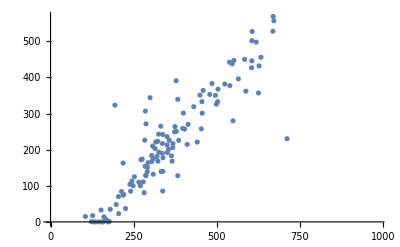

```mathematica
ListPlot[totalGasTotalHeatDaily]
```

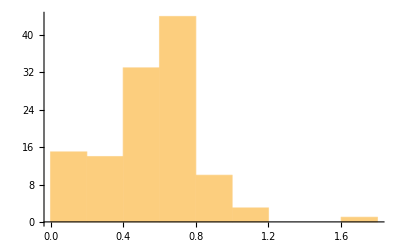

```mathematica
Histogram[Map[#[[2]]/#[[1]]&,totalGasTotalHeatDaily]]
```

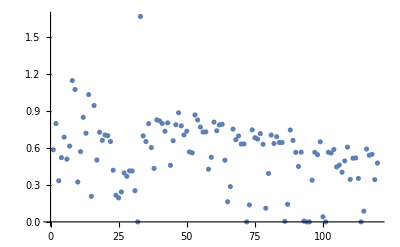

```mathematica
ListPlot[Map[#[[2]]/#[[1]]&,totalGasTotalHeatDaily]]
```

## szobák

### hőátadási tényezők becslése

```mathematica
roomsWithTempData={1,2,3,4,5,6,7,9,10};
```

```mathematica
calculationDays=Intersection[heatingStateDataDays,roomTempDataDays,externalTempDataDays];
```

#### hűlés

```mathematica
roomCoolingData=Table[Select[Flatten[Quiet[Table[
Module[
{dayN},
dayN=Position[seasonDays,day][[1]][[1]];
If[
Dimensions[roomTempsDaily[[room]][[dayN]]]!={}&&Dimensions[externalTempDaily[[dayN]]]!={}&&Dimensions[heatingStateDaily[[dayN]]]!={},
Transpose[Transpose[Select[Transpose[{
Transpose[heatingStateDaily[[dayN]][[1+roomToCycle[[room]]]]][[2]],
Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]]-Transpose[externalTempDaily[[dayN]]][[2]],
Join[{n},Differences[Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]]]/5]
}],#[[1]]==0&&#[[3]]<=0&&NumberQ[#[[2]]]&&NumberQ[#[[3]]]&]][[{2,3}]]],
None
]
]
,{day,calculationDays}]],1],Length[#]==2&],{room,1,10}];
```

```mathematica
Map[Length,roomCoolingData]
```

{20489,22185,25019,25387,14193,17439,24171,0,2320,5831}

```mathematica
roomCoolingCoefficients=Table[
Module[
{roomHeatCapacity,roomExternalWallArea,heatLossInJPerMin,heatLossInWatts,heatTransferCoefficient},
roomHeatCapacity=roomAreas[[room]]roomHeight airSpecificMass airSpecificHeatCapacity;
roomExternalWallArea=roomExternalWallLength[[room]]roomHeight;
heatLossInJPerMin=roomHeatCapacity (-Transpose[roomCoolingData[[room]]][[2]]);
heatLossInWatts=heatLossInJPerMin/60;
heatTransferCoefficient=heatLossInWatts/(roomExternalWallArea Transpose[roomCoolingData[[room]]][[1]]);
Select[heatTransferCoefficient,NumberQ]
],{room,1,10}];
```

```mathematica
roomCoolingCoefficientEstimates=Map[Mean,roomCoolingCoefficients];(*W/m2 K*)
roomCoolingCoefficientEstimates[[8]]=None;roomCoolingCoefficientEstimates
```

#### melegedés

```mathematica
heatingWaterTemperature={50,50,50,50,50,50,50,50,50,50};
roomWarmingData=Table[Select[Flatten[Quiet[Table[
Module[
{dayN},
dayN=Position[seasonDays,day][[1]][[1]];
If[
Dimensions[roomTempsDaily[[room]][[dayN]]]!={}&&Dimensions[externalTempDaily[[dayN]]]!={}&&Dimensions[heatingStateDaily[[dayN]]]!={},
Transpose[Transpose[Select[Transpose[{
Transpose[heatingStateDaily[[dayN]][[1+roomToCycle[[room]]]]][[2]],
Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]]-Transpose[externalTempDaily[[dayN]]][[2]],
heatingWaterTemperature[[room]]-Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]],
Join[{n},Differences[Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]]]/5]
}],#[[1]]==1&&-5<#[[2]]<5&&0<=#[[4]]&&NumberQ[#[[2]]]&&NumberQ[#[[4]]]&]][[{3,4}]]],
None
]
]
,{day,calculationDays}]],1],Length[#]==2&],{room,1,10}];
```

```mathematica
Map[Length,roomWarmingData]
```

{126,124,163,526,82,63,85,0,98,196}

```mathematica
roomWarmingCoefficients=Table[
Module[
{roomHeatCapacity,roomRadiatorArea,heatLossInJPerMin,heatLossInWatts,heatTransferCoefficient},
roomHeatCapacity=roomAreas[[room]]roomHeight airSpecificMass airSpecificHeatCapacity;
roomRadiatorArea=roomRadiatorLength[[room]]radiatorHeight 2;
heatLossInJPerMin=roomHeatCapacity (Transpose[roomWarmingData[[room]]][[2]]);
heatLossInWatts=heatLossInJPerMin/60;
heatTransferCoefficient=heatLossInWatts/(roomRadiatorArea Transpose[roomWarmingData[[room]]][[1]]);
Select[heatTransferCoefficient,NumberQ]
],{room,1,10}];
```

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

Power::infy: Infinite expression 1/0. encountered.

```mathematica
roomWarmingCoefficientEstimates=Map[Mean,roomWarmingCoefficients];(*W/m2 K*)
roomWarmingCoefficientEstimates[[8]]=None;
```

#### értelmezés

```mathematica
Transpose[{
roomNames,
Round[roomCoolingCoefficientEstimates,0.001],
Round[roomWarmingCoefficientEstimates,0.001]
}][[roomsWithTempData]]//Grid
```

ovi | 0.032 | 0.066
PK | 0.031 | 0.101
SZGK | 0.025 | 0.093
Gólyairoda | 0.031 | 0.205
Mérce | 0.035 | 0.078
vendégtér | 0.019 | 0.041
kisterem | 0.04 | 0.088
Oktopusz | 0.357 | 0.162
Lahmacun | 0.067 | 0.71

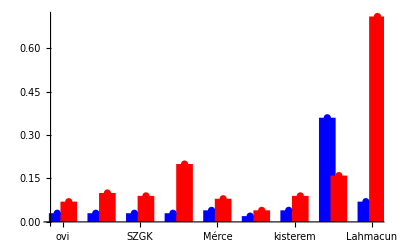

```mathematica
ListPlot[
{
Transpose[{
Range[9]-0.15,
Round[roomCoolingCoefficientEstimates,0.01][[roomsWithTempData]]
}],
Transpose[{
Range[9]+0.15,
Round[roomWarmingCoefficientEstimates,0.01][[roomsWithTempData]]
}]
},
PlotRange->All,PlotStyle->{Blue,Red},Filling->Axis,FillingStyle->{Thickness[0.03]},
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/2]&,roomNames[[roomsWithTempData]]]}],Automatic}
]
```

## hőleadás

mit:
	- hőtranszfer megbecslése egy körre egy napra csak a hőmérsékleti adatokból
sanity checkek:
	- ennek összevetése a mért hőleadással
	- leadott hő összevetése felvett hővel
	
mi látszik?
	- sok esetben jól korrelál a körön leadott teljes hő és a szobák által hőmérsékleti adatokból leadott hő
	- ami alapján meg lehet becsülni, hogy a szobák hogyan aránylanak egymáshoz
	- vagyis a mért hőleadási adatokból szét lehet osztani a hőfogyasztást szobákra

```mathematica
cycle=2;
roomsOnCycle=Flatten[Position[roomToCycle,2]];
```

Sun 31 Dec 2023 00:00:00GMT+2

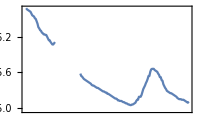
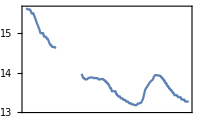
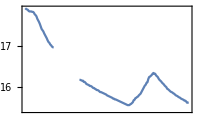
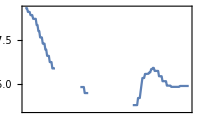

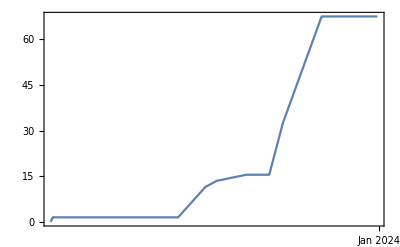
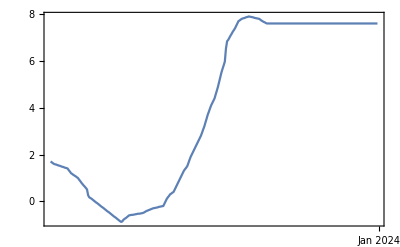

```mathematica
day=heatDataDays[[40]]
dayN=Position[seasonDays,day][[1]][[1]];
Row[Table[DateListPlot[roomTempsDaily[[room]][[dayN]][[1]],ImageSize->200],{room,roomsOnCycle}]]
Row[{DateListPlot[heatStockDaily[[cycle]][[dayN]],ImageSize->400],DateListPlot[externalTempDaily[[dayN]],ImageSize->400]}]
```

```mathematica
heatingWaterTemperature=55;
roomsHeatDynamics=Table[
Module[
{dayN},
dayN=Position[seasonDays,day][[1]][[1]];
Table[
Module[
{roomsOnCycle},
roomsOnCycle=Flatten[Position[roomToCycle,cycle]];
Table[Module[
{roomTemp,externalTemp,tempDiff,roomExternalWallArea,heatLoss,roomRadiatorArea,heatGain},
roomTemp=Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]];
externalTemp=Transpose[externalTempDaily[[dayN]]][[2]];
tempDiff=roomTemp-externalTemp;
roomExternalWallArea=roomExternalWallLength[[room]]roomHeight;
roomRadiatorArea=roomRadiatorLength[[room]]radiatorHeight 2;
heatLoss=roomCoolingCoefficientEstimates[[room]] roomExternalWallArea tempDiff;
heatGain=roomWarmingCoefficientEstimates[[room]] roomRadiatorArea (heatingWaterTemperature-roomTemp);
{
Select[Transpose[{Transpose[externalTempDaily[[dayN]]][[1]],heatLoss}],NumberQ[#[[2]]]&],
Select[Transpose[{Transpose[externalTempDaily[[dayN]]][[1]],heatGain}],NumberQ[#[[2]]]&]
}
],{room,roomsOnCycle}]
],{cycle,1,3}]
],{day,heatDataDays}];
```

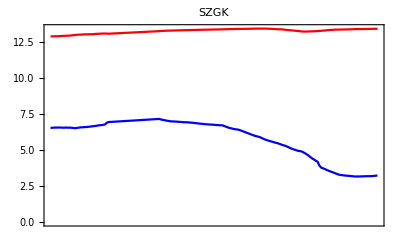
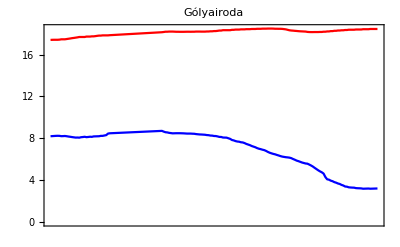
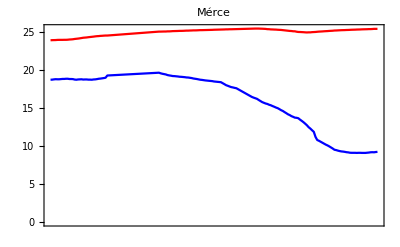
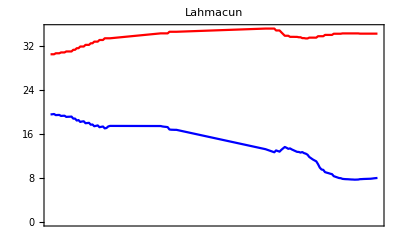

```mathematica
Table[
DateListPlot[
roomsHeatDynamics[[roomN]],PlotStyle->{Blue,Red},PlotLabel->roomNames[[roomsOnCycle[[roomN]]]]
]
,{roomN,1,Length[roomsOnCycle]}]
```

```mathematica
Total[Flatten[Map[Transpose[#][[2]]&,Transpose[roomsHeatDynamics][[1]]]]]
```

5947.38

```mathematica
Total[Flatten[Map[Transpose[#][[2]]&,Transpose[roomsHeatDynamics][[2]]]]]
```

12648.8

```mathematica
heatStockDaily[[cycle]][[dayN]][[-1]][[2]]
```

67.5

```mathematica
roomsHeatDynamics//Dimensions
```

{129,3,4,2}

```mathematica
dailyHeatSumEstimates=Quiet[Table[
Table[
{
dayN,
Total[Flatten[Map[Transpose[#][[2]]&,Transpose[roomsHeatDynamics[[dayN]][[cycle]]][[1]]]]],
Total[Flatten[Map[Transpose[#][[2]]&,Transpose[roomsHeatDynamics[[dayN]][[cycle]]][[2]]]]],
heatStockDaily[[cycle]][[dayN]][[-1]][[2]]100
},{cycle,1,3}]
,{dayN,1,Length[heatDataDays]}]];
```

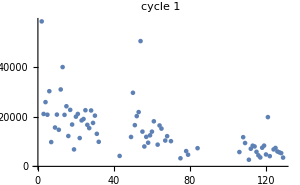
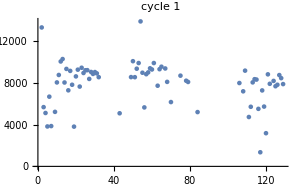
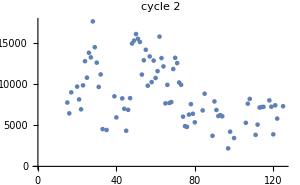
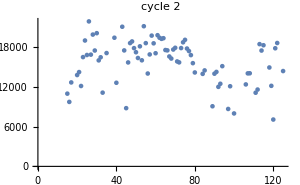

```mathematica
Table[Table[
ListPlot[
Map[#[[cycle]][[{1,1+k}]]&,dailyHeatSumEstimates]
,ImageSize->300,PlotLabel->"cycle "<>ToString[cycle]
],{k,{1,2}}],{cycle,1,2}]
```

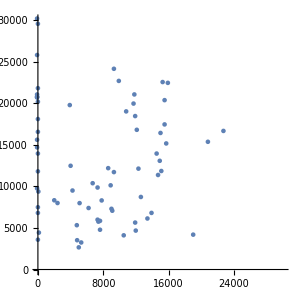
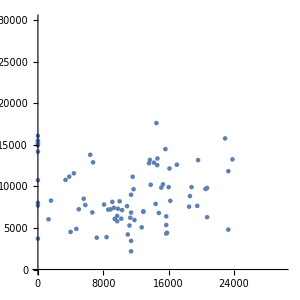
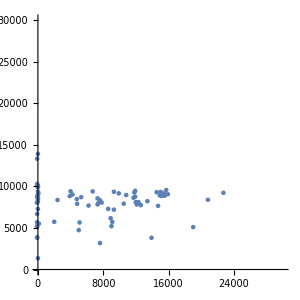
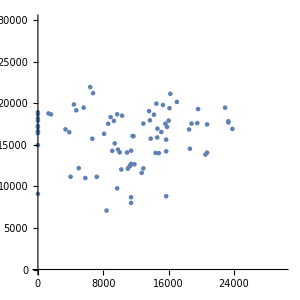

```mathematica
Table[
Table[
ListPlot[
Map[#[[cycle]][[{4,k}]]&,dailyHeatSumEstimates],ImageSize->300,PlotRange->{{0,30000},{0,30000}},AspectRatio->1
],{cycle,1,2}],{k,2,3}]
```

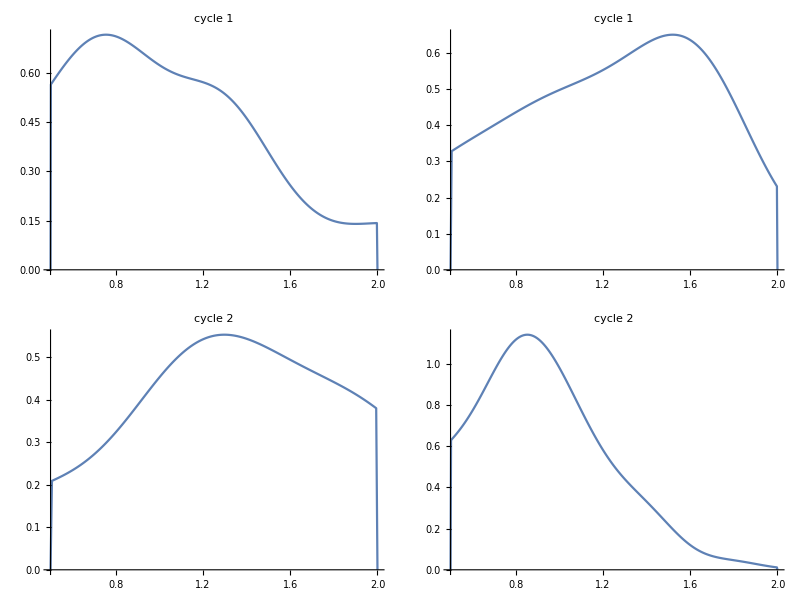

```mathematica
Table[
Table[
SmoothHistogram[
Transpose[Select[Map[#[[cycle]][[{k,4}]]&,dailyHeatSumEstimates],NumberQ[Total[#]]&&0<#[[2]]&]]//#[[2]]/#[[1]]&,
PlotRange->{{0.5,2},All},PlotLabel->"cycle "<>ToString[cycle]
]
,{k,{2,3}}]
,{cycle,1,2}]//Grid
```

```mathematica
Table[
Table[
Fit[Select[
Table[
dailyHeatSumEstimates[[dayN]][[cycle]][[{4,k}]]
,{dayN,1,Length[heatDataDays]}],NumberQ[Total[#]]&&#[[1]]>0&],{1,x},x]
,{k,{2,3}}]
,{cycle,1,2}]//Grid
```

6305.66+0.505587 x | 7285.83+0.0629854 x
6474.88+0.164126 x | 14824.9+0.0767535 x

```mathematica
Table[Select[
Table[
dailyHeatSumEstimates[[dayN]][[cycle]][[{4,2}]]
,{dayN,1,Length[heatDataDays]}],NumberQ[Total[#]]&&#[[1]]>0&]//Grid,{cycle,1,2}]
```

{9300. | 24132.4
8600. | 12186.8
9900. | 22675.7
12100. | 16796.5
13900. | 6806.65
11700. | 19951.3
11800. | 21049.1
14700. | 11364.8
11900. | 18448.4
10800. | 19010.3
15260.3 | 22538.6
22700. | 16662.6
20800. | 15355.2
15900. | 22440.4
15500. | 17445.
15500. | 20362.7
14908.3 | 13069.4
7300. | 9858.16
19000. | 4192.26
5100. | 7983.15
15100. | 11843.9
4233.33 | 9496.71
4000. | 12470.8
14526.3 | 13940.4
12600. | 8722.23
15000. | 16418.9
15700. | 15156.2
6700. | 10375.
12300. | 12128.5
8900. | 10121.4
5300. | 3249.36
13400. | 6133.44
11971.4 | 4678.78
9000. | 7298.97
7400. | 5754.79
9300. | 11712.1
56.25 | 9373.73
5000. | 2664.44
9100. | 7067.66
7800. | 8305.09
2400. | 7994.43
7600. | 5848.26
120. | 4435.24
2000. | 8324.31
7600. | 4781.1
3900. | 19770.9
10500. | 4109.88
6200. | 7394.09
7300. | 5990.77
11900. | 5643.71
4760. | 5327.59
4800. | 3523.17,5800. | 7752.59
9700. | 6443.09
11400. | 8989.36
20500. | 9684.65
9100. | 8133.26
12900. | 6932.42
15100. | 9842.23
13600. | 12777.7
3377.15 | 10772.7
6400. | 13794.6
23800. | 13241.8
14500. | 17609.
15600. | 14478.4
17000. | 12598.2
11700. | 9649.02
3833.33 | 11165.1
4000. | 4524.7
15800. | 4417.13
5600. | 8510.58
11810. | 5947.38
16200. | 8256.72
12900. | 6997.66
15700. | 4329.12
6662.03 | 6864.
1600. | 8288.23
11600. | 11151.
6750. | 12886.6
20700. | 9799.13
14623.7 | 13353.9
15300. | 10238.8
14200. | 12849.
4400. | 11565.7
22900. | 15762.5
19600. | 13150.
16100. | 12144.
19500. | 7652.02
18800. | 9902.34
8100. | 7810.89
23300. | 11824.9
13700. | 13183.
14600. | 12546.4
13800. | 10188.6
16000. | 9906.3
1300. | 6038.06
4700. | 4881.97
23300. | 4798.11
20700. | 6289.13
18500. | 7557.3
15700. | 6390.52
15700. | 5351.5
14800. | 6797.98
18600. | 8828.39
14400. | 7889.79
11400. | 6846.48
10200. | 6112.38
11300. | 6225.13
9400. | 6086.15
11400. | 2185.57
11000. | 4213.43
11400. | 3440.76
11200. | 5290.01
10900. | 7617.18
10000. | 8196.04
7200. | 3827.9
12700. | 5072.46
10300. | 7143.38
8600. | 7205.03
8900. | 7230.65
5000. | 7242.28
8400. | 3889.7
9300. | 7419.92
9700. | 5805.5
9800. | 7306.84}

## modell

- pontosítani a szobák hőtechnikai jellemzőit (homennyisegbol becsülni? figyelembe venni aktuális hőmérsékletet hokapacitashoz? fűtővíz hőmérséklete?)
- karakterizalni, h milyen költsége van  egy szoba felfutesenek adott külső hőmérséklet mellett 
- jellemezni a szitut költség - komfort síkon, akár szezonon belül is
- modellezni, hogy szabályozás vagy beavatkozás mennyit tol a síkon milyen irányba